```mathematica
<< xAct`xCoba`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
DefManifold[M,4,IndexRange[a,q]];
DefChart[ch,M,{0,1,2,3},{t[],x[],y[],z[]},ChartColor -> Blue];
DefConstantSymbol[mass, PrintAs-> "M"];
```

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

** DefChart: Defining chart ch.

** DefTensor: Defining coordinate scalar t[].

** DefTensor: Defining coordinate scalar x[].

** DefTensor: Defining coordinate scalar y[].

** DefTensor: Defining coordinate scalar z[].

** DefMapping: Defining mapping ch.

** DefMapping: Defining inverse mapping ich.

** DefTensor: Defining mapping differential tensor dich[-a,icha].

** DefTensor: Defining mapping differential tensor dch[-a,cha].

** DefBasis: Defining basis ch. Coordinated basis.

** DefCovD: Defining parallel derivative PDch[-a].

** DefTensor: Defining vanishing torsion tensor TorsionPDch[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDch[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDch[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDch[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpch[a,b,c,d].

** DefTensor: Defining antisymmetric -1 density etaDownch[-a,-b,-c,-d].

** DefConstantSymbol: Defining constant symbol mass.

```mathematica
$Assumptions = mass >0 && x[]∈Reals&& y[]∈Reals && z[]>1 && t[]∈Reals; 
gg=CTensor[{{-1/Sqrt[z[]],0,0,0},{0,z[],0,0},{0,0,z[],0},{0,0,0,1/Sqrt[z[]]}},{-ch,-ch}];
SetCMetric[gg,ch,SignatureOfMetric->{3,1,0}];
cd=CovDOfMetric[gg];

gmatrix= ComponentArray[gg[{-a,-ch},{-b,-ch}]] // MatrixForm;
```

```mathematica
weyl=Weyl[cd][{-a,-ch},{-b,-ch},{-c,-ch},{-d,-ch}];
```

```mathematica
(*La base tetrada*)
(*La base tetrada*)
l=CTensor[{Sqrt[1]/Sqrt[2Sqrt[z[]]],0,0,Sqrt[1]/Sqrt[2Sqrt[z[]]]},{-ch}];
n=CTensor[{Sqrt[1]/Sqrt[2Sqrt[z[]]],0,0,-Sqrt[1]/Sqrt[2Sqrt[z[]]]},{-ch}];
m=CTensor[{0, Sqrt[z[]]/Sqrt[2],I Sqrt[z[]]/Sqrt[2],0},{-ch}];
mb=CTensor[{0, Sqrt[z[]]/Sqrt[2],-I Sqrt[z[]]/Sqrt[2],0},{-ch}];
```

```mathematica
n[a]m[-a]//Simplify
```

0

```mathematica
(*Se define el Killing*)
k=CTensor[{1,0,0,0},{ch}];

F= cd[-b]@k[-a]//Simplify;
F=Head[F];
Fd= F[-a,-b]+I/2 epsilon[gg][-a,-b,e,f]F[-e,-f];
Fd= Head[Fd];
```

```mathematica
σ= 2Fd[-a,-b]k[b]//Simplify;
σ=Head[σ];
```

```mathematica
σ[-a]
```

0
0
0
-1/(2 z^(3/2)) |  
a

```mathematica
DefScalarFunction[sg];
```

** DefScalarFunction: Defining scalar function sg.

```mathematica
cd[-a]@sg[z[]]==σ[-a]
```

e |   | 3
a |   sg'[z]==0
0
0
-1/(2 z^(3/2)) |  
a

e |   | 3
a |   sg'[z]==0
0
0
-1/(2 z^(3/2)) |  
a

e |   | 3
a |   sg'[z]==0
0
0
-1/(2 z^(3/2)) |  
a

```mathematica
DSolve[sg'[z[]]==-1/(2 z[]^(3/2)),{sg[z[]]},{z[]}]
```

Attributes::notfound: Symbol DSolveDispatchODE not found.

{{sg[z]→C[1]+1/(√z)}}

```mathematica
σE= 1+1/Sqrt[z[]] ;
```

```mathematica
(*Componentes del tensor de Weyl*)
ps0= -Weyl[cd][-a,-b,-c,-d]l[a]m[b]l[c]m[d]// Simplify;
ps1= -Weyl[cd][-a,-b,-c,-d]l[a]n[b]l[c]m[d]// Simplify;
ps2= 1/2 Weyl[cd][-a,-b,-c,-d](l[a]n[b]l[c]n[d]+l[a]n[b]m[c]mb[d])// Simplify;
ps3= Weyl[cd][-a,-b,-c,-d]l[a]n[b]n[c]mb[d]// Simplify;
ps4= -Weyl[cd][-a,-b,-c,-d]n[a]mb[b]n[c]mb[d]// Simplify;
```

```mathematica
0
```

0

```mathematica
ps2
```

1/(8 z^(3/2))

```mathematica
(*Definos las matrices alpha*)
α1=m[-a]mb[-b]-mb[-a]m[-b]+l[-a]n[-b]-n[-a]l[-b] // Simplify;
α2= -l[-a] mb[-b]+mb[-a] l[-b]+m[-a] n[-b]-n[-a] m[-b] // Simplify;
α3= I(l[-a] mb[-b]-mb[-a] l[-b]+m[-a] n[-b]-n[-a] m[-b])// Simplify;
```

```mathematica
DefManifold[S3,3,{P,Q,S,R,T}];
DefChart[ch3,S3,{0,1,2},{u[],v[],w[]},ChartColor -> Red];


(*Métrica δ_ij=identidad 3x3*)
g3=CTensor[{{1,0,0},{0,1,0},{0,0,1}},{-ch3,-ch3}];
SetCMetric[g3,ch3,SignatureOfMetric->{0,3,0}];
cd3=CovDOfMetric[g3];

g3matrix= ComponentArray[g3[{-P,-ch3},{-Q,-ch3}]] // MatrixForm;
```

** DefManifold: Defining manifold S3.

** DefVBundle: Defining vbundle TangentS3.

** DefChart: Defining chart ch3.

** DefTensor: Defining coordinate scalar u[].

** DefTensor: Defining coordinate scalar v[].

** DefTensor: Defining coordinate scalar w[].

** DefMapping: Defining mapping ch3.

** DefMapping: Defining inverse mapping ich3.

** DefTensor: Defining mapping differential tensor dich3[-e,ich3P].

** DefTensor: Defining mapping differential tensor dch3[-P,ch3e].

** DefBasis: Defining basis ch3. Coordinated basis.

** DefCovD: Defining parallel derivative PDch3[-P].

** DefTensor: Defining vanishing torsion tensor TorsionPDch3[P,-Q,-R].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDch3[P,-Q,-R].

** DefTensor: Defining vanishing Riemann tensor RiemannPDch3[-P,-Q,-R,S].

** DefTensor: Defining vanishing Ricci tensor RicciPDch3[-P,-Q].

** DefTensor: Defining antisymmetric +1 density etaUpch3[P,Q,R].

** DefTensor: Defining antisymmetric -1 density etaDownch3[-P,-Q,-R].

```mathematica
Head[α3]//FullSimplify
```

CTensor[{{0,0,z^(1/4),0},{0,0,0,-ⅈ z^(1/4)},{-z^(1/4),0,0,0},{0,ⅈ z^(1/4),0,0}},{-ch,-ch},0]

```mathematica
(*Se crea ya si con los índices internos IJ en la subvariedad*)
Alpha=CTensor[{{{0,0,0,-1/(√z)},{0,0,-ⅈ z,0},{0,ⅈ z,0,0},{1/(√z),0,0,0}},{{0,-z^(1/4),0,0},{z^(1/4),0,0,0},{0,0,0,-ⅈ z^(1/4)},{0,0,ⅈ z^(1/4),0}},{{0,0,z^(1/4),0},{0,0,0,-ⅈ z^(1/4)},{-z^(1/4),0,0,0},{0,ⅈ z^(1/4),0,0}}},{ch3,-ch,-ch}]//Simplify;
```

```mathematica
(*Se define la matriz H_IJ*)
H=1/16 Alpha[-P,-a,-b]Alpha[-Q,-c,-d]Weyl[cd][a,b,c,d] // Simplify;
```

```mathematica
FI=Alpha[P,-a,-b]k[b]σ[a]//Simplify;
FI=Head[FI];
```

```mathematica
FI[P]//FullSimplify
```

-1/(2 z^(3/2))
0
0 | P

```mathematica
ve=CTensor[{1,0,0},{ch3}];
```

```mathematica
FI[P]ve[-P]
```

-1/(2 z^(3/2))

```mathematica
fff=6(FI[-P]ve[P]FI[-P]ve[P]-4/3FI[P]FI[-P]);
```

```mathematica
fff=3/8(Alpha[P,-a,-b]Fd[a,b]ve[-P]Alpha[P,-a,-b]Fd[a,b]ve[-P]-4/3Fd[-a,-b]Fd[a,b])//FullSimplify
```

1/(8 z^2)

```mathematica
L= 4ps2/fff;
```

```mathematica
L
```

4 √z

```mathematica
q=Abs[L+1/σE]^2 / (Abs[L]+Abs[1/σE])^2//Simplify
```

1

```mathematica
qq=ComplexExpand[Abs[q]]//Simplify
```

1

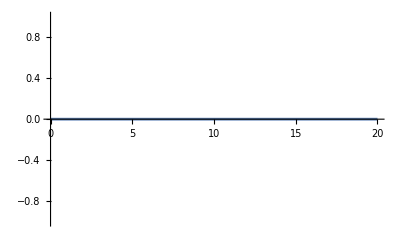

```mathematica
Plot[1-q,{z,0,20}]
```

```mathematica
6L(FI[-P]FI[-Q]-1/3 FI[S]FI[-S]g3[-P,-Q])==  H[-P,-Q]
```

-1/z^(3/2) | 0 | 0
0 | 1/(2 z^(3/2)) | 0
0 | 0 | 1/(2 z^(3/2)) |   |  
P | Q==1/(8 z^(3/2)) | 0 | 0
0 | -1/(16 z^(3/2)) | 0
0 | 0 | -1/(16 z^(3/2)) |   |  
Q | P[-P,-Q]

```mathematica
H[-P,-Q]
```

1/(8 z^(3/2)) | 0 | 0
0 | -1/(16 z^(3/2)) | 0
0 | 0 | -1/(16 z^(3/2)) |   |  
Q | P[-P,-Q]

```mathematica
cd[-b]@k[-a]+cd[-a]@k[-b]//Simplify
```

0

```mathematica
Conjugate[L]L//FullSimplify
```

z^3

```mathematica
L//Simplify
```

-z^(3/2)

```mathematica
cd[-b]@k[-a]+cd[-a]@k[-b]//FullSimplify
```

0

1/(8 z^2)

```mathematica
L=4ps2/fff//FullSimplify
```

4 √z

```mathematica
-1/σE
```

-1/(1+1/(√z))

```mathematica
Fd[-a,-b]Fd[a,b]//FullSimplify
```

-1/(4 z^2)

```mathematica
Alpha[P,-a,-b]Fd[a,b]ve[-P]Alpha[P,-a,-b]Fd[a,b]ve[-P]//FullSimplify
```

0

```mathematica
(*Comprobacion de killing*)
```

```mathematica
cd[-b]@k[-a]+ cd[-a]@k[-b]
```

0